# ColorGraphEdges

Color the edges of a graph so no edges incident to each other have the same color

## Definition

```mathematica
ClearAll[ColorGraphEdges]
ColorGraphEdges[graph_?GraphQ,options:OptionsPattern[Graph]]:=Graph[Annotate[graph,{EdgeStyle->Thread[EdgeList[graph]->FindEdgeColoring[graph,ColorData[106,"ColorList"]]]}],options];

ColorGraphEdges[graph_?GraphQ,colors_List,options:OptionsPattern[Graph]]:=Graph[Annotate[graph,{EdgeStyle->Thread[EdgeList[graph]->FindEdgeColoring[graph,colors]]}],options]
```

## Documentation

### Usage

ColorGraphEdges[graph]

Color the edges of graph so no edges incident to each other have the same color

ColorGraphVertices[graph, colors]

Color the edges of graph so no edges incident to each other have the same color with colors.

### Details & Options

The vertices are colored using ColorData[106] by default.

Finding colorings for graphs is an NP complete area of combinatorial research.

## Examples

### Basic Examples

Color the edges of the Petersen graph:

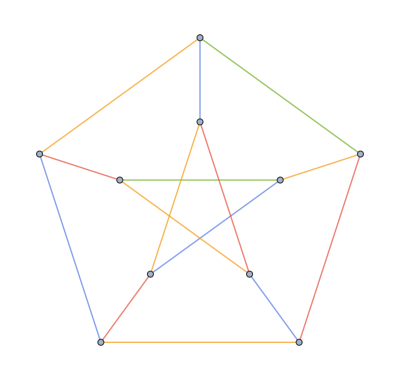

```mathematica
ColorGraphEdges[PetersenGraph[]]
```

Use a different coloring list with ColorData:

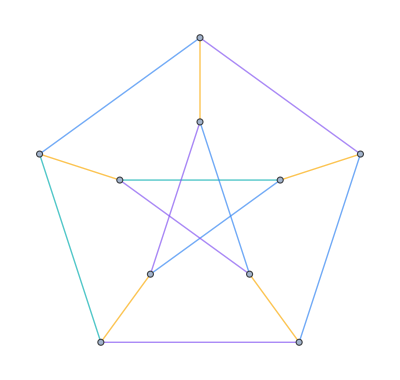

```mathematica
ColorGraphEdges[PetersenGraph[],ColorData[101,"ColorList"]]
```

### Scope

Color the edges of the skeleton of the Csaszar polyhedron:

```mathematica
ColorGraphEdges@MeshConnectivityGraph[PolyhedronData["CsaszarPolyhedron","Polyhedron"],0]
```

-Graphics3D-

### Possible Issues

Sometimes the function FindEdgeColoring cannot find an edge coloring

FindEdgeColoring::invc: Unable to find a coloring of the graph with less than 43 colors.

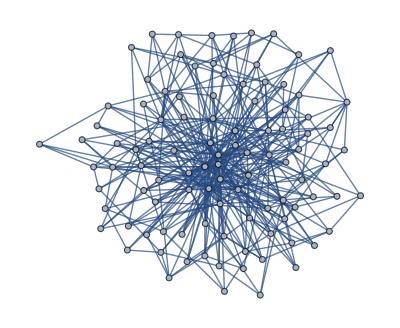

```mathematica
ColorGraphEdges[RandomGraph[BarabasiAlbertGraphDistribution[101,4]]]
```

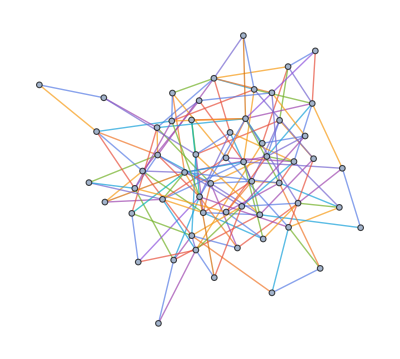

```mathematica
ColorGraphEdges[RandomGraph[{57,154}],ImageSize->Full]
```

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Graph coloring

Four Color Theorem

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FindVertexColoring

FindEdgeColoring

FindIndependentEdgeSet

### Related Resource Objects

RandomMixedGraph

AlternatingTreeGraph

RandomWeightedGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.